## 基本图形对象

在 Wolfram 语言中，Circle[ ] 表示一个圆。要将圆显示为图形，要使用函数 Graphics。稍后，我们将看到如何指定一个圆的位置和大小。但现在，我们只要处理一个基本的圆，它不需要任何额外的输入。

创建一个圆的图形：

```mathematica
Graphics[Circle[ ]]
```

-Graphics-

Disk 表示一个被填充的圆盘：

```mathematica
Graphics[Disk[ ]]
```

-Graphics-

RegularPolygon 将创建由你指定的边数的正多边形。

这里是一个正五边形：

```mathematica
Graphics[RegularPolygon[5]]
```

-Graphics-

创建边数为 5 到 10 之间的正多边形的图形列表：

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Style 可以用在 Graphics 内，所以你可以用它来给定颜色。

这里是一个橙色的五边形：

```mathematica
Graphics[Style[RegularPolygon[5],Orange]]
```

-Graphics-

Wolfram 语言可以在三维和二维中工作，有诸如 Sphere、Cylinder 和 Cone 等结构。当你拥有三维图形时，你可以交互式地旋转它们以查看不同的角度。

以三维方式显示一个球体：

```mathematica
Graphics3D[Sphere[ ]]
```

-Graphics3D-

一个圆锥体和圆柱体的列表：

```mathematica
{Graphics3D[Cone[ ]],Graphics3D[Cylinder[ ]]}
```

{-Graphics3D-,-Graphics3D-}

一个黄色的球体：

```mathematica
Graphics3D[Style[Sphere[ ],Yellow]]
```

-Graphics3D-

词汇

Circle[ ] |   | 指定一个圆
Disk[ ] |   | 指定一个实心圆盘
RegularPolygon[n] |   | 指定一个边数为 n 的正多边形
Graphics[object] |   | 将对象显示为图形
Sphere[ ], Cylinder[ ], Cone[ ], ... |   | 指定三维几何形状
Graphics3D[object] |   | 将对象显示为 3D 图形

"共有 8 道习题"
"以及 3 道附加题" | "开始练习 »"

使用 RegularPolygon 来绘制一个三角形。»

| 期望输出： |  
  |  |

绘制红色圆圈的图形。»

| 期望输出： |  
  |  |

创建红色的八边形。»

| 期望输出： |  
  |  |

创建一个列表，其元素是色相以步长为 0.1 从 0 变化到 1 的圆盘。»

| 期望输出： |  
  | {,,,,,,,,,,} |

创建一个红色和绿色三角形的列。»

| 期望输出： |  
  | 
 |

创建边数为 5 到 10 的正多边形，每个多边形都为粉色。»

| 期望输出： |  
  | {,,,,,} |

创建紫色圆柱的图形。»

| 期望输出： |  
  | -Graphics3D- |

创建一个包含 8、7、6...3 条边的多边形列表，并使用 RandomColor 进行着色。然后将它们全部与最上层的三角形进行重叠(提示：对列表应用 Graphics)。»

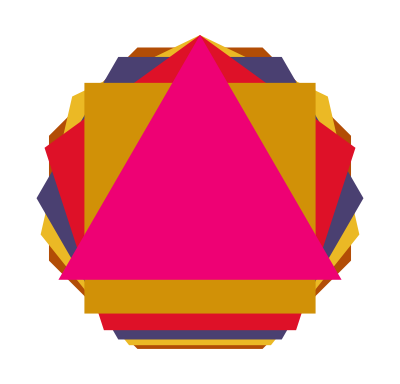
| 期望输出示例： |  
  | -Graphics- |

创建一个列表，其中包含 10 个随机颜色的正五边形。»

| 期望输出： |  
  | {,,,,,,,,,} |

创建一个列表，包含一个正二十边形和一个圆盘。»

| 期望输出： |  
  | {,} |

创建一个包含 10、9...3 条边的正多边形列表。»

| 期望输出： |  
  | {,,,,,,,} |

问&答

我怎样才能创建包含多个对象的图形？

第 14 节会进行解释，要做到这一点，需要先了解坐标。

为什么要使用 Circle[ ]，而不是直接用 Circle？

为了保持一致性。正如我们将在第 14 节看到的，Circle[ ] 实际上是 Circle[{0,0},1] 的缩略形式，它表示一个半径为 1、中心坐标为 {0,0} 的圆。

为什么黄色球体不是纯黄色？

因为 Wolfram 语言使它看起来就像一个实际的三维物体，带有光照。如果它是纯黄色的，你就不会看到任何三维深度，看起来就像一个二维圆盘。

技术笔记

另一种为图形指定样式的方法是在一个列表中给出“指令”，例如 {Yellow,Disk[ ],Black,Circle[ ]}。

探索更多

Wolfram 语言中的图形指南 »